```mathematica
ClearGlobal[];
```

```mathematica
$Assumptions={ {Lx, Ly, Lz}∈Reals, Lx>0, Ly>0, Lz>0, L>0, Ixx>0};
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["Calc3DMatProp`"]
```

## Geometry and topology definition

```mathematica
nodes={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,0,1},{0,1,1},{1,1,0},{1,1,1},{1/2,1/2,1/2},{1/2,0,1/2},{0,1/2,1/2},{1/2,1,1/2},{1,1/2,1/2},{1/2,1/2,0},{1/2,1/2,1}}L;
beams={{3,1},{1,2},{2,7},{7,3},{4,5},{5,8},{8,6},{6,4},{1,4},{2,5},{7,8},{3,6},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8}};
shells={{10,1,2},{10,2,5},{10,5,4},{10,4,1},{11,1,3},{11,3,6},{11,6,4},{11,4,1},{12,3,6},{12,6,8},{12,8,7},{12,7,3},{13,7,8},{13,8,5},{13,5,2},{13,2,7},{14,1,2},{14,2,7},{14,7,3},{14,3,1},{15,4,5},{15,5,8},{15,8,6},{15,6,4},{9,7,3},{9,7,8},{9,8,6},{9,6,3},{9,5,2},{9,4,1},{9,1,2},{9,4,5},{9,7,2},{9,1,3},{9,5,8},{9,4,6}};
nnodes=Dimensions[nodes]⟦1⟧;
nbeams=Dimensions[beams]⟦1⟧;
a1=nodes⟦2⟧-nodes⟦1⟧;a2=nodes⟦3⟧-nodes⟦1⟧;a3=nodes⟦4⟧-nodes⟦1⟧;
V=a1.a2×a3;
{αs,βs,γs}={(Es (ν-1))/(2 ν^2+ν-1),-(Es ν)/(2 ν^2+ν-1),Es/(2 ν+2)};
```

```mathematica
Eqs={{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}};
(* Eqs={{1,1,1,1,1,1,1,1,0}};*)
{B0,Bϵ}=MakeB0andBe[Eqs,nodes]//Simplify;
```

```mathematica
rbeams={{3},{4},{5},{6},{7},{8},{10},{11},{12}};
rshells={{9},{10},{11},{12},{13},{14},{15},{16},{21},{22},{23},{24}};
```

```mathematica
ρ=CalcModelVolume[nodes, Delete[beams,rbeams],Delete[shells,rshells],  {A, 2 Iyy, Iyy, Iyy},{Es,ν,t}]/V//Simplify;
```

```mathematica
Graph1=DrawUnitCell[nodes/.{ L->1}, beams,shells]
Graph2=DrawUnitCell[nodes/.{ L->1},  Delete[beams,rbeams],Delete[shells,rshells]]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* Export["cubicCellBCC.eps",Rasterize[Graph1, ImageResolution->600,Background->None]]
Export["cubicCellPrimBCC.eps",Rasterize[Graph2, ImageResolution->600,Background->None]] *)
```

## Find material stiffness matrix

### Only beams

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2 Iyy, Iyy, Iyy},{Es,ν,t},{1,0,0}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L^2/(A Es)Kmat/.{Iyy->0}//Simplify//MatrixForm
```

(1+4/(3 √3) | 4/(3 √3) | 4/(3 √3) | 0 | 0 | 0
4/(3 √3) | 1+4/(3 √3) | 4/(3 √3) | 0 | 0 | 0
4/(3 √3) | 4/(3 √3) | 1+4/(3 √3) | 0 | 0 | 0
0 | 0 | 0 | 4/(3 √3) | 0 | 0
0 | 0 | 0 | 0 | 4/(3 √3) | 0
0 | 0 | 0 | 0 | 0 | 4/(3 √3))

```mathematica
L^4/(Es Iyy)Kmat/.{ A->0}//Simplify//MatrixForm
```

(128/(3 √3) | -64/(3 √3) | -64/(3 √3) | 0 | 0 | 0
-64/(3 √3) | 128/(3 √3) | -64/(3 √3) | 0 | 0 | 0
-64/(3 √3) | -64/(3 √3) | 128/(3 √3) | 0 | 0 | 0
0 | 0 | 0 | 6+32/(3 √3) | 0 | 0
0 | 0 | 0 | 0 | 6+32/(3 √3) | 0
0 | 0 | 0 | 0 | 0 | 6+32/(3 √3))

### Only shells

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{0,1,0}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L/(Es t) Kmat//Simplify//MatrixForm
```

((4+3 √2)/(2-2 ν^2) | (√2+4 (1+√2) ν)/(4-4 ν^2) | (√2+4 (1+√2) ν)/(4-4 ν^2) | 0 | 0 | 0
(√2+4 (1+√2) ν)/(4-4 ν^2) | (4+3 √2)/(2-2 ν^2) | (√2+4 (1+√2) ν)/(4-4 ν^2) | 0 | 0 | 0
(√2+4 (1+√2) ν)/(4-4 ν^2) | (√2+4 (1+√2) ν)/(4-4 ν^2) | (4+3 √2)/(2-2 ν^2) | 0 | 0 | 0
0 | 0 | 0 | (2+3 √2-2 (1+√2) ν)/(4-4 ν^2) | 0 | 0
0 | 0 | 0 | 0 | (2+3 √2-2 (1+√2) ν)/(4-4 ν^2) | 0
0 | 0 | 0 | 0 | 0 | (2+3 √2-2 (1+√2) ν)/(4-4 ν^2))

### Only plates

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{0,0,1}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L^3/(Es t^3)Kmat//Simplify//MatrixForm
```

((82 √2)/(9-9 ν^2) | (41 √2)/(9 (-1+ν^2)) | (41 √2)/(9 (-1+ν^2)) | 0 | 0 | 0
(41 √2)/(9 (-1+ν^2)) | (82 √2)/(9-9 ν^2) | (41 √2)/(9 (-1+ν^2)) | 0 | 0 | 0
(41 √2)/(9 (-1+ν^2)) | (41 √2)/(9 (-1+ν^2)) | (82 √2)/(9-9 ν^2) | 0 | 0 | 0
0 | 0 | 0 | (9 (272+189 √2)-6 (128+81 √2) ν-64 ν^2)/(54 (-7+2 ν) (-1+ν^2)) | 0 | 0
0 | 0 | 0 | 0 | (9 (272+189 √2)-6 (128+81 √2) ν-64 ν^2)/(54 (-7+2 ν) (-1+ν^2)) | 0
0 | 0 | 0 | 0 | 0 | (9 (272+189 √2)-6 (128+81 √2) ν-64 ν^2)/(54 (-7+2 ν) (-1+ν^2)))

### Everything

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{1,1,1}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
```

```mathematica
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
{α, β, γ}={Kmat[[1,1]], Kmat[[1,2]], Kmat[[6,6]]};
BeamForces=Table[GetBeamForces[kk,dϵ.{1,0,0,0,0,0}, nodes,beams,{Es,Es/(2(1+ν))},{A, 2 Iyy, Iyy, Iyy}], {kk,1,nbeams}];
```

### Some plots

```mathematica
{α,β,γ}={Kmat⟦1,1⟧,Kmat⟦1,2⟧,Kmat⟦6,6⟧};
```

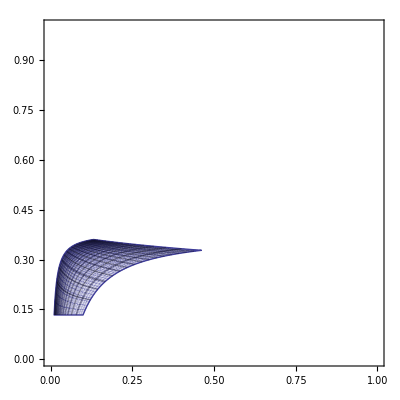

```mathematica
ParametricPlot[Simplify[Evaluate[{ρ,(α+2 β)/((αs+2 βs)ρ)}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5},PlotRange->{{0,1},{0,1}},AspectRatio->Full]
```

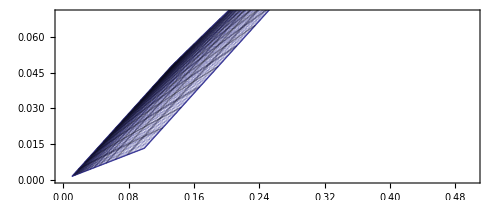

```mathematica
ParametricPlot[Simplify[Evaluate[{ρ,(α+2 β)/(αs+2 βs)}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5},PlotRange->{{0,0.5},{0,0.07}},AspectRatio->Full]
```

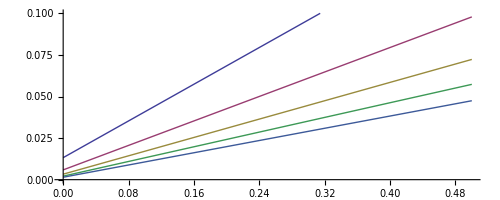

```mathematica
Plot[Evaluate[Table[Simplify[(α+2 β)/(αs+2 βs)/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30,5}]],{λ2,0,0.5},PlotRange->{{0,0.5},{0,0.1}},AspectRatio->Full]
```

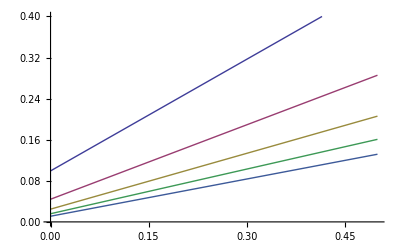

```mathematica
Plot[Evaluate[Table[Simplify[ρ/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30,5}]],{λ2,0,.5}, PlotRange->{0, 0.4}]
```

### Element stresses

```mathematica
Cmat=Inverse[Kmat]//Simplify;
```

```mathematica
Cmat[[1,1]]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}//Simplify
```

(7 λ1^2 (135 (46+41 √2) λ1^3 λ2+273 (9+8 √3) λ1^2+12300 √2 λ1 λ2^3+1456 √3))/(Es (60 (1+√2) λ1 λ2+7 (3+4 √3)) (45 (34+19 √2) λ1^3 λ2+819 λ1^2+12300 √2 λ1 λ2^3+1456 √3))

```mathematica
BeamStress=Simplify[Table[GetBeamStress[kk,dϵ.Cmat.{1,1,1,0,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}],{kk,1,nbeams}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}];
```

```mathematica
BeamBuckl=Simplify[Table[GetBeamBuckl[kk,dϵ.Cmat.{1,1,1,0,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}],{kk,1,nbeams}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}];
```

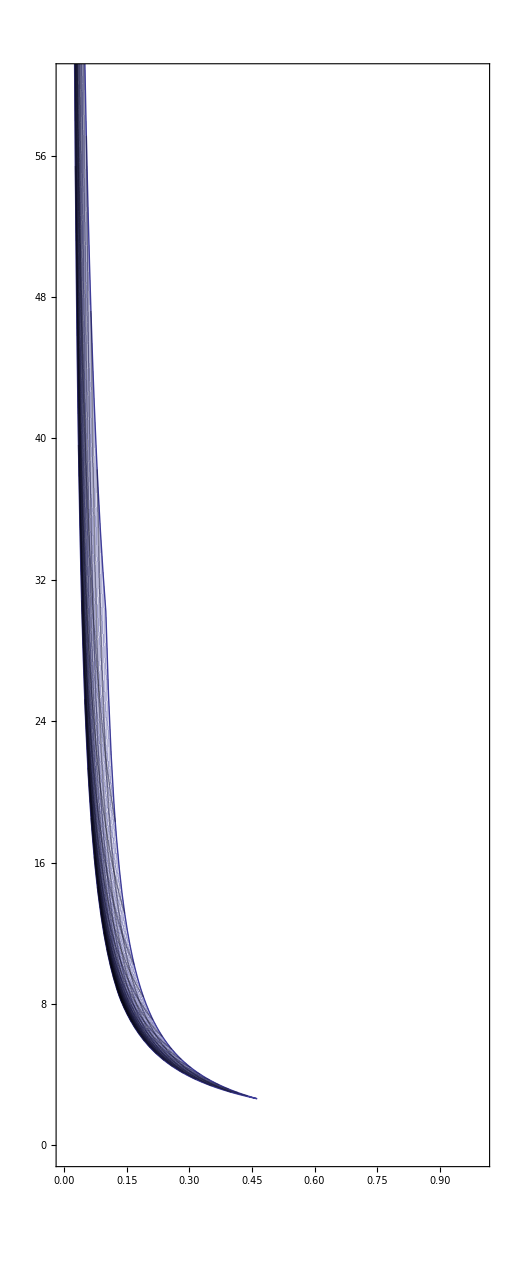

```mathematica
ParametricPlot[Simplify[Evaluate[{ρ,BeamStress[[1,1]]}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5},PlotRange->{{0,1},{0,60}},AspectRatio->Full]
```

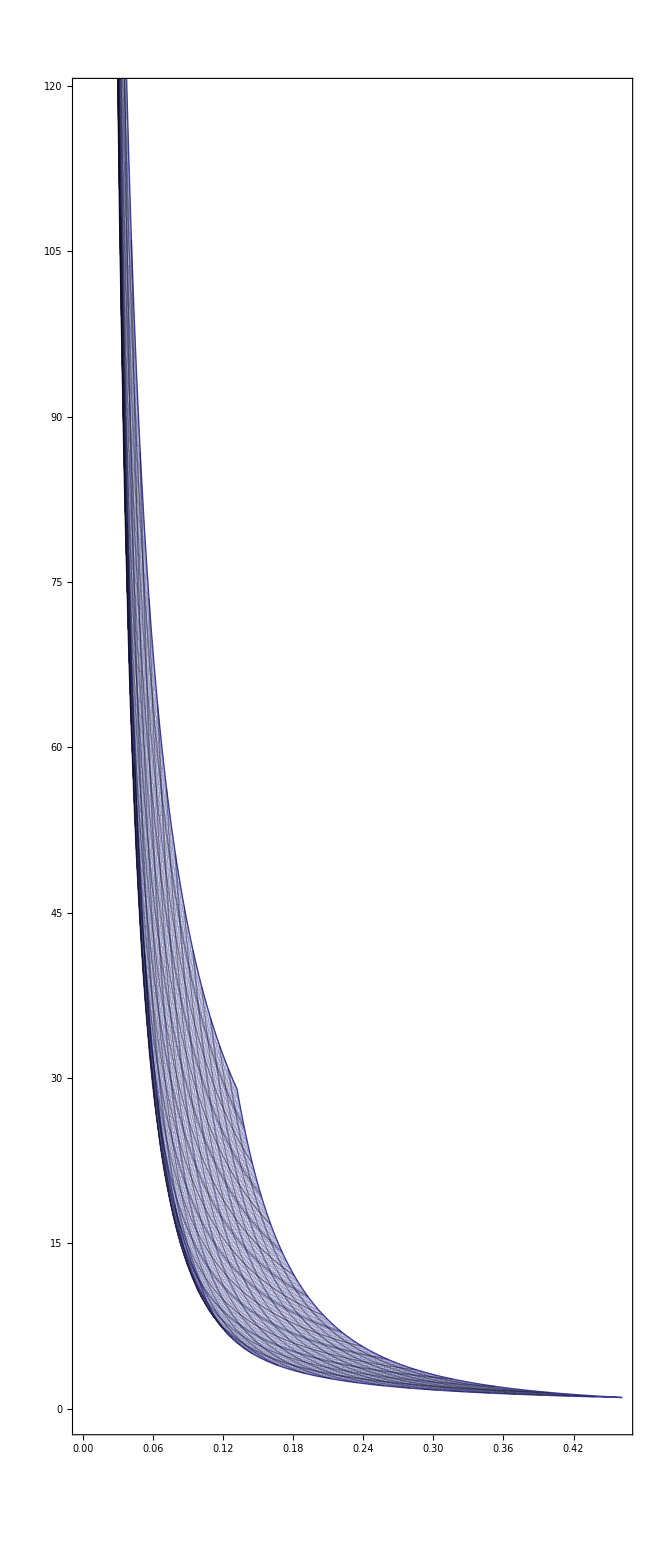

```mathematica
ParametricPlot[Simplify[Evaluate[{ρ,BeamBuckl[[1,1]]/10^3}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5}, AspectRatio->Full]
```

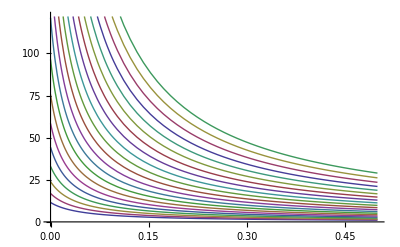

```mathematica
Plot[Evaluate[Table[Simplify[BeamBuckl[[1,1]]/10^3/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30}]],{λ2,0,.5}]
```